```mathematica
2. n=20 [-1,2]
```

```mathematica
Grid[  Table[{(x),(Cos[2x]),(       ∑_(i=0)^20 ((-4)^(i)x^(2i))/((2i)!)), Abs[(Cos[2x]-       ∑_(i=0)^20 ((-4)^(i)  x^(2i))/((2i)!))],(Cos[2x]-       ∑_(i=0)^20 ((-4)^(i) x^(2i))/((2i)!))}, {x, -1, 2, .4}]]
```

-1. | -0.416147 | -0.416147 | 5.55112×10^-17 | 5.55112×10^-17
-0.6 | 0.362358 | 0.362358 | 1.11022×10^-16 | 1.11022×10^-16
-0.2 | 0.921061 | 0.921061 | 0. | 0.
0.2 | 0.921061 | 0.921061 | 1.11022×10^-16 | 1.11022×10^-16
0.6 | 0.362358 | 0.362358 | 5.55112×10^-17 | 5.55112×10^-17
1. | -0.416147 | -0.416147 | 5.55112×10^-17 | 5.55112×10^-17
1.4 | -0.942222 | -0.942222 | 2.22045×10^-16 | 2.22045×10^-16
1.8 | -0.896758 | -0.896758 | 2.22045×10^-16 | -2.22045×10^-16

Observation of Accuracy : The fourth column in the table above gives the absolute difference between Cos(2x) and the Taylor polynomial of degree 20 from -1 to 2. It can be seen that the difference is very small from -1 to 2 with the highest recorded difference being 2.22045×10^-16. This means that this Taylor polynomial of degree 20 is a very good approximation of Cos(2x) from -1 to 2. The highest difference is recorded at x values of 1.4 and 1.8. Although this difference is very small, it can be seen that it is increasing as the x values are farther away from the center, which is 0.

```mathematica
2. n=20 [-1,1]
```

```mathematica
Grid[  Table[{(x),(Cos[2x]),(       ∑_(i=0)^20 ((-4)^(i) x^(2i))/((2i)!)), Abs[(Cos[2x]-       ∑_(i=0)^20 ((-4)^(i) x^(2i))/((2i)!))],(Cos[2x]-       ∑_(i=0)^20 ((-4)^(i)x^(2i))/((2i)!))}, {x, -1, 1, .4}]]
```

-1. | -0.416147 | -0.416147 | 5.55112×10^-17 | 5.55112×10^-17
-0.6 | 0.362358 | 0.362358 | 1.11022×10^-16 | 1.11022×10^-16
-0.2 | 0.921061 | 0.921061 | 0. | 0.
0.2 | 0.921061 | 0.921061 | 1.11022×10^-16 | 1.11022×10^-16
0.6 | 0.362358 | 0.362358 | 5.55112×10^-17 | 5.55112×10^-17
1. | -0.416147 | -0.416147 | 5.55112×10^-17 | 5.55112×10^-17

Observation of Accuracy : The fourth column in the table above gives the absolute difference between Cos(2x) and the Taylor polynomial of degree 20 from -1 to 1. The difference is very small from -1 to 1 with the highest recorded difference being 1.11022×10^-16. This means that this Taylor polynomial of degree 20 is a very good approximation of Cos(2x) from -1 to 1.

```mathematica
2. n=30 [-1,2]
```

```mathematica
Grid[  Table[{(x),(Cos[2x]),(       ∑_(i=0)^30 ((-4)^(i)x^(2i))/((2i)!)), Abs[(Cos[2x]-       ∑_(i=0)^30 ((-4)^(i) x^(2i))/((2i)!))],(Cos[2x]-       ∑_(i=0)^30 ((-4)^(i)x^(2i))/((2i)!))}, {x, -1, 2, .4}]]
```

-1. | -0.416147 | -0.416147 | 5.55112×10^-17 | 5.55112×10^-17
-0.6 | 0.362358 | 0.362358 | 1.11022×10^-16 | 1.11022×10^-16
-0.2 | 0.921061 | 0.921061 | 0. | 0.
0.2 | 0.921061 | 0.921061 | 1.11022×10^-16 | 1.11022×10^-16
0.6 | 0.362358 | 0.362358 | 5.55112×10^-17 | 5.55112×10^-17
1. | -0.416147 | -0.416147 | 5.55112×10^-17 | 5.55112×10^-17
1.4 | -0.942222 | -0.942222 | 2.22045×10^-16 | 2.22045×10^-16
1.8 | -0.896758 | -0.896758 | 2.22045×10^-16 | -2.22045×10^-16

Observation of Accuracy : The fourth column in the table above gives the absolute difference between Cos(2x) and the Taylor polynomial of degree 30 from -1 to 2. The difference is very small from -1 to 2 with the highest recorded difference being 2.22045×10^-16. This means that this Taylor polynomial of degree 30 is a very good approximation of Cos(2x) from -1 to 2. The highest difference is recorded at x values of 1.4 and 1.8. Although this difference is very small, it can be seen that it is increasing as the x values are farther away from the center, which is 0.

```mathematica
2. n=30 [-1,1]
```

```mathematica
Grid[  Table[{(x),(Cos[2x]),(       ∑_(i=0)^30 ((-4)^(i)x^(2i))/((2i)!)), Abs[(Cos[2x]-       ∑_(i=0)^30 ((-4)^(i) x^(2i))/((2i)!))],(Cos[2x]-       ∑_(i=0)^30 ((-4)^(i)x^(2i))/((2i)!))}, {x, -1, 1, .4}]]
```

-1. | -0.416147 | -0.416147 | 5.55112×10^-17 | 5.55112×10^-17
-0.6 | 0.362358 | 0.362358 | 1.11022×10^-16 | 1.11022×10^-16
-0.2 | 0.921061 | 0.921061 | 0. | 0.
0.2 | 0.921061 | 0.921061 | 1.11022×10^-16 | 1.11022×10^-16
0.6 | 0.362358 | 0.362358 | 5.55112×10^-17 | 5.55112×10^-17
1. | -0.416147 | -0.416147 | 5.55112×10^-17 | 5.55112×10^-17

Observation of Accuracy : The fourth column in the table above gives the absolute difference between Cos(2x) and the Taylor polynomial of degree 30 from -1 to 1. The difference is very small from -1 to 1 with the highest recorded difference being 1.11022×10^-16. This means that this Taylor polynomial of degree 30 is a very good approximation of Cos(2x) from -1 to 1.

```mathematica
Assignment:
```

1. Write the general form of the Taylor polynomial expansion of the function,Cos(2x) at c=0. 

The general form of the Taylor polynomial expansion of the function Cos(2x) at c = 0 is given by, P_n(x)=   ∑_(i=0)^n ((-4)^i *x^(2i))/((2i)!).
 
2. Modify the program for degrees n =  20 and 30, and  the intervals [-1, 2], [-1,1]. Provide a single table for each degree with x-values incremented by .4. Comment on the accuracy of the approximations. 

	All four graphs contained very small differences, which means that their approximations for Cos(2x) on their respective intervals are all very good. Despite the change in interval and degrees, the differences for the same x values were identical across all four tables. This could be because the polynomials of degree 20 and 30 are both very good estimates for Cos(2x) on both [-1,1] and [-1,2]. Upon seeing that the differences are virtually the same, I decided to graph the Taylor polynomials and f(x) = cos(2x) in order to visually see these differences. I have included this plot at the end of the investigation since it shows that the polynomial of degree 30 has a larger range of very small error than the polynomial of degree 20. 
	The differences across polynomials of the same degree did not differ based on their different intervals. The fact that they did not differ could be due to the intervals being very close to the center, which has an exact error of zero. Since these polynomials are of very large degree, 20 and 30, it is expected that their approximations would be very accurate for intervals 1 or 2 points from the center. The largest difference between two points was in the range of 10^-17, which is very significant because it is a very small error to allow despite being the largest. This small error makes it a good option to use either of these polynomials to approximate f(x) = Cos(2x) on [-1,1] or [-1,2].   
	In addition, the tables with intervals [-1,2] showed the differences increasing as the x values grew farther from the center, which is at 0. This trend was visible because of the larger interval in comparison to the interval [-1,1]. The difference of 0 at -0.2 also shows this since that x value is very close to the center, which has an exact error of 0. This supports our previous knowledge in the way the Taylor polynomial was constructed with its center at 0.  Overall, the approximations across all polynomials of differing degrees are all very accurate on their respective intervals.

2. Supplemental Graph

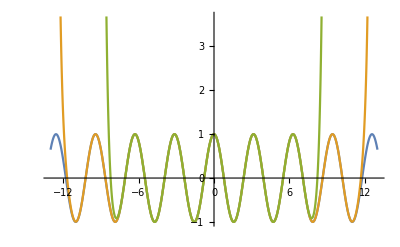

```mathematica
Plot[{Cos[2x],        ∑_(i=0)^30 ((-4)^i *x^(2i))/((2i)!),        ∑_(i=0)^20 ((-4)^i *x^(2i))/((2i)!)},{x, -13, 13}]
```